# Mathematica Notebook for “Cultural evolution by capital accumulation” by J.B. André and N. Baumard

## Model 1

### Phase 1 : Learning and growth

```mathematica
ClearAll["Global`*"]
P[x_,y_]:=x^α y^β
Px[x_,y_]:= x^(-1+α) y^β α
Py[x_,y_]:=x^α y^(-1+β) β
```

the return on the allocation of each unit of time to growth is therefore

```mathematica
Px[x,y]γ
```

and the return on the allocation of each unit of time to learning is

```mathematica
Py[x,y]λ
```

so the optimal allocation function is such that we will always maintain

```mathematica
Solve[λ Py[x,y]==γ Px[x,y],y]//FullSimplify
```

{{y→(x β λ)/(α γ)}}

so we’re going to maintain a ratio y/x = (β λ)/(α γ)

which therefore implies an investment l in learning such as

```mathematica
Solve[λ l ==γ  (1-l)(β λ)/(α γ),l]//FullSimplify
```

{{l→β/(α+β)}}

In what follows, we introduce a parameter c measuring the relative importance of culture, with  β = c and α = 1-c

We will also later use the parameter κ=c/(1-c)

```mathematica
ClearAll["Global`*"]

DSolve[{x'[t]==γ (1-c),y'[t]==λ c ,x[0]==0,y[0]==0},{x[t],y[t]},t]
```

{{x[t]→t γ-c t γ,y[t]→c t λ}}

so the growth of y at a rate of  λ c lasts until y=z, which gives us

```mathematica
t1[z_]:=z/(λ c)
```

so at the end of this period we have 

y:=z
x:=(γ (1-c))/(λ c)z

the ratio between the two types of capital is  κ:=y/x=(λ c)/(γ (1-c))

### Phase 2 : Pure growth

then x will grow on its own until we reach the new ratio :

```mathematica
y/x:=(η c)/(γ(1-c))
```

so x is going to grow at a rate to go from (γ (1-c))/(λ c)z to (γ (1-c))/(η c)z

which is going to take the time

```mathematica
((γ (1-c))/(η c)-(γ (1-c))/(λ c))z/γ//FullSimplify
```

```mathematica
t2[z_]:=((1-c) (λ-η))/(c η λ)z
```

and so in all it takes a time t to reach the frontier with t=t1+t2

```mathematica
((1-c) (λ-η))/(c η λ)z+z/(λ c)//FullSimplify
```

```mathematica
Simplify[((1-c)/η+c/λ)z/c==((1-c) (λ-η))/(c η λ)z+z/(λ c)]
```

True

```mathematica
κ:=c/(1-c);
Simplify[(1/(η κ)+1/λ)z==((1-c) (λ-η))/(c η λ)z+z/(λ c)]
```

True

```mathematica
t[z_]:=((1-c)/η+c/λ)z/c
```

### Phase 3 : Innovation at the frontier

once we get to the frontier, we’ve got the ratio that must remain constant y/x:=(η c)/(γ(1-c))

```mathematica
Solve[η (1/ratio)^(1-c)  c==γ (ratio)^c (1-c),ratio]//FullSimplify
```

{{ratio→(c η)/(γ-c γ)}}

```mathematica
Solve[{λ l==η d(N-1),γ(1-d-l)==(γ (1-c))/(η c)η N d},{l,d}]//FullSimplify
```

{{l→(c (-1+N) η)/(c (-1+N) (η-λ)+N λ),d→(c λ)/(c (-1+N) (η-λ)+N λ)}}

```mathematica
Solve[{λ l==η d(N-1),(λ l+η d)/(γ(1-d-l))==(η κ)/γ},{l,d}]//FullSimplify
```

{{l→(c (-1+N) η)/(c (-1+N) (η-λ)+N λ),d→(c λ)/(c (-1+N) (η-λ)+N λ)}}

So the total growth rate of z during innovation is given by ri:=λl+ηd=ηdN

```mathematica
η N (c λ)/(c (-1+N) (η-λ)+N λ)//FullSimplify
```

(c N η λ)/(c (-1+N) (η-λ)+N λ)

```mathematica
ri:=(c N η λ)/(c (N-1) (η-λ)+N λ)
```

### Plot of entire development of individuals (Figure 1 of paper)

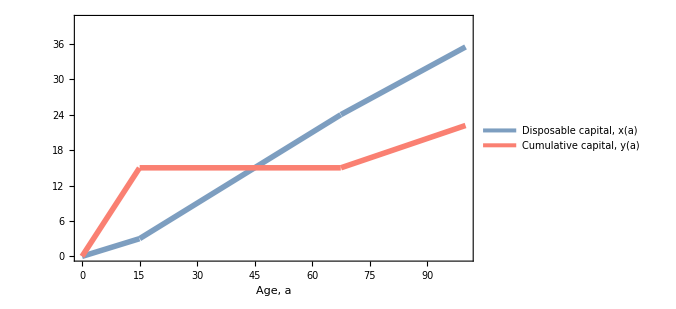

```mathematica
rx1:=γ/(1+κ)
ry1:=(λ κ)/(1+κ)

ry2:=0
rx2:=γ

l:=((-1+PopSize) η κ)/((-1+PopSize) η κ+(PopSize+κ) λ)
d:=(κ λ)/((-1+PopSize) η κ+(PopSize+κ) λ)

ry3:=η d PopSize 

rx3:=γ (1-d-l)

τ1:=z/λ(1+κ)/κ
τ2:=(λ-η)/(λ η κ)z

γ:=0.4
λ:=2
κ:=1
η:=0.25

PopSize:=100

L:=100

z:=15

zmax:=40;
xmax:=40;

MyTicks={FontFamily->"Avenir",FontSize->8};
MyLabel={FontFamily->"Avenir",FontSize->12};

XColor=lightblue;
YColor=salmon;

cobalt="#3D59AB";
tomato3="#CD4F39";
salmon="#FA8072";
lightblue="#7D9EC0";

XStyle={Thickness[0.008],RGBColor[XColor]};
YStyle={Thickness[0.008],RGBColor[YColor]};

x:=Function[t,If[t<τ1,rx1 t,If[t<τ1+τ2,rx1 τ1 + rx2 (t-τ1),rx1 τ1 +rx2 τ2+rx3 (t-τ1-τ2)]]];

y:=Function[t,If[t<τ1,ry1 t,If[t<τ1+τ2,ry1 τ1 + ry2 (t-τ1),ry1 τ1 +ry2 (τ2-τ1)+ry3 (t-τ1-τ2)]]];

Plot[{x[t],y[t]},{t,0,L},PlotRange->{{0,L},{0,zmax}},Frame->True,Axes->False,PlotStyle->{XStyle,YStyle},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{"Age, a", "","",""},LabelStyle->MyLabel,PlotLegends->Placed[{"Disposable capital, x(a)", "Cumulative capital, y(a)"},Below],FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->500]
```

### Plot of cultural dynamics (Figure 2 of paper)

```mathematica
ClearAll["Global`*"]
Newz:=z+(L-τ)r
r:=(N η κ λ)/((-1+N) η κ+(N+κ) λ)
τ:=(λ+η κ)/(λ η κ)z
Newz//FullSimplify
```

(κ (L N η λ+z (-η+λ)))/((-1+N) η κ+(N+κ) λ)

```mathematica
RSolve[{z[t+1]==(κ (L N η λ+z[t] (-η+λ)))/((-1+N) η κ+(N+κ) λ),z[0]==0},z[t],t]//FullSimplify
```

{{z[t]→-(L η κ λ (-1+((κ (-η+λ))/((-1+N) η κ+(N+κ) λ))^t))/(η κ+λ)}}

```mathematica
Simplify[(λ  η κ)/(λ+η κ)L(1-(1+(λ + η κ)/(κ (λ-η))N)^-t)==-(L η κ λ (-1+((κ (-η+λ))/((-1+N) η κ+(N+κ) λ))^t))/(η κ+λ)]
```

(L η κ λ (((κ (-η+λ))/((-1+N) η κ+(N+κ) λ))^t-(1+(N (η κ+λ))/(κ (-η+λ)))^-t))/(η κ+λ)==0

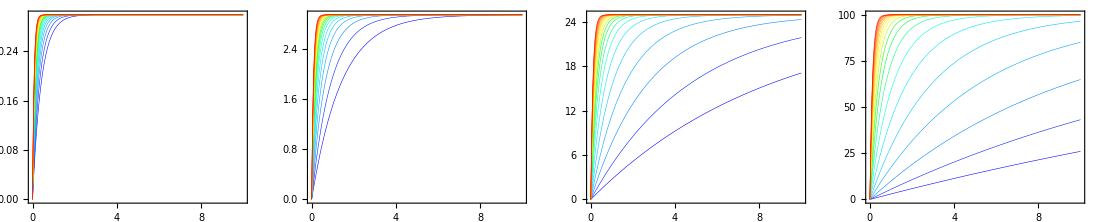

```mathematica
ClearAll["Global`*"]

z[t_,NPop_]:=(λ  η κ)/(λ+η κ)L(1-(1+(λ + η κ)/(κ (λ-η))NPop)^-t)

γ:=1
λ:=5
η:=0.1
L:=30

Tmax=10;

NbCurves=20;

TColor={"#FF0a00","#FF3200","#FF5000","#FF6e00","#FF8c00","#FFaa00","#FFc800","#FFe600","#fdff00","#b0ff00","#17ff00","#00ff36","#00ff83","#00ffd0","#00e4ff","#00c4ff","#00a4ff","#0084ff","#0022ff","#0500ff"};

MyTicksStyle={FontFamily->"Avenir",FontSize->6};
MyLabel={FontFamily->"Avenir",FontSize->6};

Variableκ={0.1,1,10,100 };
mySize=200;
MyAspectRatio=1;

δ=0.9;
For[ii=1,ii≤4,ii++,

κ=Variableκ[[ii]];

TCurves=Table[z[t,(1+δ)^ii],{ii,0,NbCurves-1}];
TStyles=Table[{Thickness[0.002],RGBColor[TColor[[NbCurves-i]]]},{i,0,NbCurves-1}];

Subscript[P, ii]=Plot[TCurves,{t,0,Tmax},Frame->True,Axes->False,PlotRange->{{0,Tmax},All},
PlotStyle->TStyles,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{MyTicksStyle,MyTicksStyle,MyTicksStyle,MyTicksStyle},ImageSize->mySize,AspectRatio->MyAspectRatio];
(***************************************)
];
GraphicsRow[Table[Subscript[P, ii],{ii,1,5}]]
```

### Analysis of the cumulative potential of a population

here I will analyze the gap between the growth rate of culture in the innovation phase, ri, and the growth rate in the catch-up phase, rc; the greater the gap between the two, the greater the cumulative potential

```mathematica
ri:=(λ η κ N)/((N+κ) λ +(N-1) η κ)
rc:=(λ  η κ)/(λ+η κ)
```

which becomes

```mathematica
ri:=(λ η κ)/(λ+η κ + κ/N(λ-η))
rc:=(λ  η κ)/(λ+η κ)
```

So we can see that the two expressions are identical except for the κ/N(λ-η) at the denominator of ri ==>

So what’s really important is whether or not  κ/N(λ-η) is negligible in front of  λ+η κ 

To understand further ==>

```mathematica
ClearAll["Global`*"]
Newz=ri L+z (1-ri/rc)//FullSimplify

RSolve[{z[t+1]==ri L+z[t] (1-ri/rc),z[0]==0},z[t],t]//FullSimplify
```

L ri+z-(ri z)/rc

{{z[t]→-L rc (-1+(1-ri/rc)^t)}}

```mathematica
Simplify[L rc (1-(1-ri/rc)^t)==-L rc (-1+(1-ri/rc)^t)]
```

so it’s clear that what measures the cumulative potential is the parameter

```mathematica
1-ri/rc
```

that becomes

```mathematica
(rc-ri)/rc
```

This gives ==>

```mathematica
ClearAll["Global`*"]

ri:=(λ η κ N)/(λ (N+κ)+η κ(N-1))
rc:=(λ η κ)/(λ+η κ)
(rc-ri)/ri//FullSimplify
```

```mathematica
ClearAll["Global`*"]
K=(κ (-η+λ))/(N (η κ+λ))
κ:=c/(1-c)
K//FullSimplify
```

(κ (-η+λ))/(N (η κ+λ))

```mathematica
Simplify[(c (λ-η))/(λ-c (λ-η))1/N==(c (λ-η))/(λ-c (λ-η))1/N]
```

True

```mathematica
ClearAll["Global`*"]

ri:=(λ η κ N)/(λ (N+κ)+η κ(N-1))
rc:=(λ η κ)/(λ+η κ)
Newz=ri L+z (1-ri/rc)//FullSimplify
```

(κ (L N η λ+z (-η+λ)))/((-1+N) η κ+(N+κ) λ)

## Model 2

## Functions to evaluate before for once

```mathematica
(* Implicit in this model : 
Growth[Q_]:= γ Q ;
Learning[Q_]:=λ Q ;
Innovating[Q_]:=η Q;
*)
```

These are numerical simulations: at each step of time the individuals put all their resources where it is the most useful.

==> at the frontier they either (i) put everything into the growth of x or (ii) everything into a combination of innovation+learning 
in this second case it is necessary to calculate the fraction that they put in innovation ==> this fraction must respect

```mathematica
Solve[η P d(N-1)==λ P (1-d),d]//FullSimplify
```

{{d→λ/((-1+N) η+λ)}}

so the growth rate of y at the frontier is η d P N, which gives

```mathematica
ClearAll["Global`*"]
P[x_,y_]:=((x^((1-c[x])δ))(y^((c[x])δ)))
D[P[x,y],y]
```

x^(δ (1-c[x])) y^(-1+δ c[x]) δ c[x]

```mathematica
ClearAll["Global`*"]

(*
δ est le diminishing return ; si δ=1 alors on a un constant return ; si δ<1 alros on a diminishing return ; si δ>1 alors on a increasing return 
*)

P[x_,y_,z0_]:=((x^((1-c[x])δ))(y^((c[x])δ)))+P0[z0]

Px[x_,y_]:= -x^(-1+δ-δ c[x]) y^(δ c[x]) δ (-1+c[x]+x (Log[x]-Log[y]) c'[x])
Py[x_,y_]:=x^(δ-δ c[x]) y^(-1+δ c[x]) δ c[x]

xIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[γ thisPx≥λs thisPy,res=γ thisP δt,res=0],
If[γ thisPx≥η thisPy,res=γ thisP δt,res=0]];res];


yIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[λs thisPy > γ thisPx,res=Min[λs thisP δt, z0-y],res=0],
If[η thisPy > γ thisPx,res= (η *λf* thisP * PopSize)/(λf+η(PopSize-1)) δt,res=0]];res];

(*Newz function*)
Newz:=Function[z0,
x=N[10^-10];
y=N[10^-10];
For[t=0,t<LifeSpan,t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]]];
y
];

(*Newz function*)
Adultx:=Function[z0,
x=N[10^-10];
y=N[10^-10];
For[t=0,t<LifeSpan,t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]]];
x
];

Deltaz[z_]:=Newz[z]-z
```

## Results (with Figures of paper)

Basic results (Figure 3 and 4 of paper)

### Individual Growth

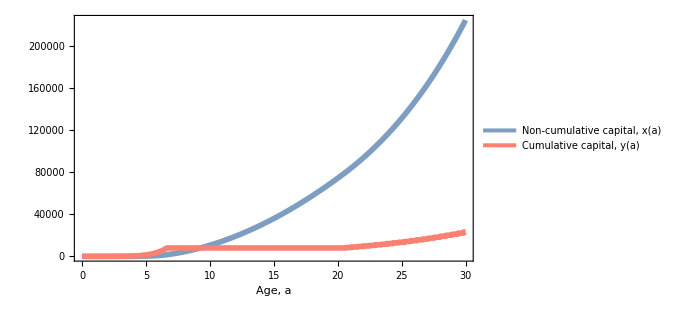

Final x = 224114. ; Final y =  23183.4

```mathematica
(**************Parameters*******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;
c0=0.5;

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
(**************End of Parameters*******)

z0=8000;

x=N[10^-10];
y=N[10^-10];
X={{0,x}};
Y={{0,y}};
Ratio={{0,1}};

For[t=0,t<LifeSpan,

thisTimeStep=TimeStep;

t+=thisTimeStep;

x+= N[xIncrease[x,y,z0,thisTimeStep] ];
y+= N[yIncrease[x,y,z0,thisTimeStep] ];

X=Append[X,{t,x}];
Y=Append[Y,{t,y}];
Ratio=Append[Ratio,{t,N[y/x]}];

(*Print[η Py[x,y] ," ", γ Px[x,y]];*)
];

MyTicks={FontFamily->"Avenir",FontSize->10};
MyLabel={FontFamily->"Avenir",FontSize->12};

XColor=lightblue;
YColor=salmon;

cobalt="#3D59AB";
tomato3="#CD4F39";
salmon="#FA8072";
lightblue="#7D9EC0";

XStyle={Thickness[0.008],RGBColor[XColor]};
YStyle={Thickness[0.008],RGBColor[YColor]};

ListLinePlot[{X,Y},Axes->False,Frame->True,PlotRange->All,PlotStyle->{XStyle,YStyle},FrameLabel->{"Age, a", "","",""},LabelStyle->MyLabel,PlotLegends->Placed[{"Non-cumulative capital, x(a)", "Cumulative capital, y(a)"},Below],FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->500]

Print["Final x = ", x, " ; Final y =  ", y];
```

### Population cultural Growth (Figure 3 of paper)

#### Varying c

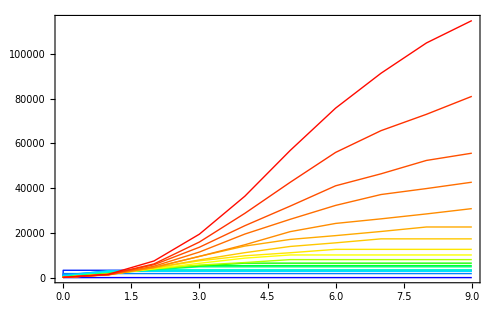

```mathematica
(**************Parameters*******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;

(*c0=0.5;*)

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
(**************End of Parameters*******)

MaxGenerations=10;

ZDynamics:=Function[fractionCulture,
c0=fractionCulture;

z=0;
Z={{0,z}};

For[g=0,g<MaxGenerations,

z=Newz[z];
Z=Append[Z,{g,z}];
g+=1;
];
Z];

TColor={"#FF0a00","#FF3200","#FF5000","#FF6e00","#FF8c00","#FFaa00","#FFc800","#FFe600","#fdff00","#b0ff00","#17ff00","#00ff36","#00ff83","#00ffd0","#00e4ff","#00c4ff","#00a4ff","#0084ff","#0022ff","#0500ff"};

TVariable=Table[0.025*ii,{ii,0,19}];
NbCurves=Length[TVariable];

TCurves=Table[ZDynamics[TVariable[[ii]]],{ii,1,NbCurves}];
TStyles=Table[{Thickness[0.002],RGBColor[TColor[[NbCurves-i]]]},{i,0,NbCurves-1}];

ListLinePlot[TCurves,Frame->True,Axes->False,PlotRange->All,
PlotStyle->TStyles,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{MyTicksStyle,MyTicksStyle,MyTicksStyle,MyTicksStyle},ImageSize->500]
```

#### Varying δ

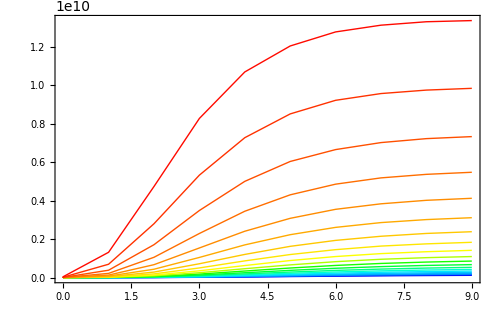

```mathematica
(**************Parameters*******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;

c0=0.5;

(*δ=0.9;*)

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
(**************End of Parameters*******)

MaxGenerations=10;

ZDynamics:=Function[fractionCulture,
c0=fractionCulture;

z=0;
Z={{0,z}};

For[g=0,g<MaxGenerations,

z=Newz[z];
Z=Append[Z,{g,z}];
g+=1;
];
Z];

TColor={"#FF0a00","#FF3200","#FF5000","#FF6e00","#FF8c00","#FFaa00","#FFc800","#FFe600","#fdff00","#b0ff00","#17ff00","#00ff36","#00ff83","#00ffd0","#00e4ff","#00c4ff","#00a4ff","#0084ff","#0022ff","#0500ff"};

TVariable=Table[0.85+0.005*ii,{ii,0,19}];
NbCurves=Length[TVariable];

TCurves=Table[ZDynamics[TVariable[[ii]]],{ii,1,NbCurves}];
TStyles=Table[{Thickness[0.002],RGBColor[TColor[[NbCurves-i]]]},{i,0,NbCurves-1}];

ListLinePlot[TCurves,Frame->True,Axes->False,PlotRange->All,
PlotStyle->TStyles,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{MyTicksStyle,MyTicksStyle,MyTicksStyle,MyTicksStyle},ImageSize->500]
```

#### Varying LifeSpan

```mathematica
(**************Parameters*******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;

c0=0.5;

δ=0.9;

PopSize=1000;
(*LifeSpan=30;*)
TimeStep=0.01;
(**************End of Parameters*******)
MyTicksStyle={FontFamily->"Avenir",FontSize->6};
MaxGenerations=20;

ZDynamics:=Function[L,
LifeSpan=L;

z=0;
Z={{0,z}};

For[g=0,g<MaxGenerations,

z=Newz[z];
Z=Append[Z,{g,z}];
g+=1;
];
Z];

TColor={"#FF0a00","#FF3200","#FF5000","#FF6e00","#FF8c00","#FFaa00","#FFc800","#FFe600","#fdff00","#b0ff00","#17ff00","#00ff36","#00ff83","#00ffd0","#00e4ff","#00c4ff","#00a4ff","#0084ff","#0022ff","#0500ff"};

TVariable=Table[20+ii,{ii,0,19}];
NbCurves=Length[TVariable];

TCurves=Table[ZDynamics[TVariable[[ii]]],{ii,1,NbCurves}];
TStyles=Table[{Thickness[0.002],RGBColor[TColor[[NbCurves-i]]]},{i,0,NbCurves-1}];

PDynamics=ListLinePlot[TCurves,Frame->True,Axes->False,PlotRange->All,
PlotStyle->TStyles,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{MyTicksStyle,MyTicksStyle,MyTicksStyle,MyTicksStyle},ImageSize->250,AspectRatio->1]
```

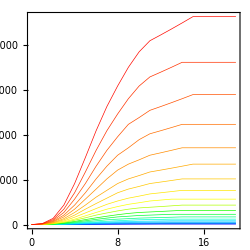

```mathematica
MyTicksStyle={FontFamily->"Avenir",FontSize->6};PDynamics=ListLinePlot[TCurves,Frame->True,Axes->False,PlotRange->All,
PlotStyle->TStyles,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameTicksStyle->{MyTicksStyle,MyTicksStyle,MyTicksStyle,MyTicksStyle},ImageSize->250,AspectRatio->1]
```

### z’ in function of z (Figure 4a of paper)

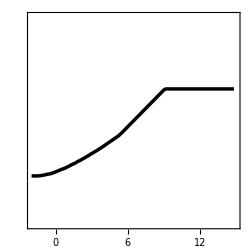

```mathematica
(**************Parameters*******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;
c0=0.5;

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
(**************End of Parameters*******)


NbPoints=100;

(*LOG*)
logzmin=-2;
logzmax=15;

TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/NbPoints}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/NbPoints}];

MyTicks={Black,FontFamily->"Avenir",FontSize->6};
MyLabel={Black,FontFamily->"Avenir",FontSize->12};
MyRange={{logzmin,logzmax},{logzmin,logzmax}};

seashell="#8B8682";

ZStyle={Thickness[0.005],RGBColor[seashell],Dashing[{0.000001,0.008}]};
NewZStyle={Black,Thickness[0.01]};


(*FrameLabel->{"Amount of cumulative capital in t, z_t (Log_10)","Amount of cumulative capital in t+1, z_(t + 1) (Log_10)"}*)

(*PNewz=Show[ListLinePlot[{Table[{TLogZ[[i]],TLogZ[[i]]},{i,1,NbPoints}],Table[{TLogZ[[i]],TLogNewz[[i]]},{i,1,NbPoints}]},PlotRange->MyRange,PlotStyle->{ZStyle,NewZStyle}],LabelStyle->MyLabel,Frame->True,Axes->False,FrameLabel->{None,None,None,None},FrameTicks->{Automatic, None,None, None},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->250, AspectRatio->1]*)

PNewz=Show[ListLinePlot[{Table[{TLogZ[[i]],TLogNewz[[i]]},{i,1,NbPoints}]},PlotRange->MyRange,PlotStyle->{NewZStyle}],LabelStyle->MyLabel,Frame->True,Axes->False,FrameLabel->{None,None,None,None},FrameTicks->{Automatic, None,None, None},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->250, AspectRatio->1]
```

### Dynamic Landscape (Figure 4b of paper)

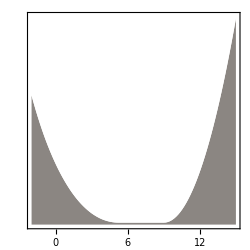

```mathematica
(************** Parameters *******)
c[x_]:=c0
P0[z_]:=P00

γ=1;
λs=5;
λf=5;
η=0.1;
P00=0.1;
c0=0.5;

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
(************** End of Parameters *******)

NbPoints=100;

BackgroundColor=white;
GroundColor=seashell;

seashell="#8B8682";
white="#ffffff";

MyAspectRatio=1;

(*LOG*)

logzmin=-2;
logzmax=15;

TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];

TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (TLogZ[[k]]-TLogNewz[[k]])+GroundLevel},{i,1,NbPoints}];

TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={Black,FontFamily->"Avenir",FontSize->6};

(*FrameLabel->{"Amount of knowledge, z (Log_10)", "Dynamic Landscape"}*)
PLandscape=Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameLabel->{None, None},FrameTicks->{Automatic, None, None, None},LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->250,AspectRatio->MyAspectRatio]
```

Effect of c[x] (Figure 5a-d of paper)

#### parameters

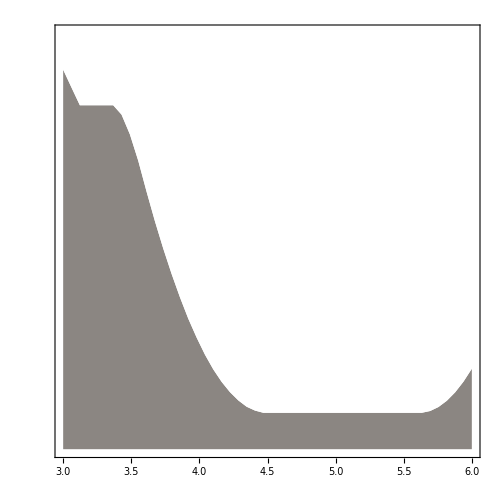

```mathematica
(************** Parameters *******)
P0[z_]:=P00

c[x_]:=If[x<ThresholdX,cmin,cmax]

cmin=0.05;
cmax=0.5;
ThresholdX=300000;

γ=1;
λf=5;
λs=5;
η=0.1;
P00=0.1;

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;
NbPoints=100;

(************** End of Parameters *******)

BackgroundColor=white;
GroundColor=seashell;

seashell="#8B8682";
white="#ffffff";

logzmin=3;
logzmax=6;

TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];
TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->10};

Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameLabel->None,LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicks->{Automatic,None,None,None},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->500, AspectRatio->1]
```

#### Variation of cmax (Figure 5a-d of paper)

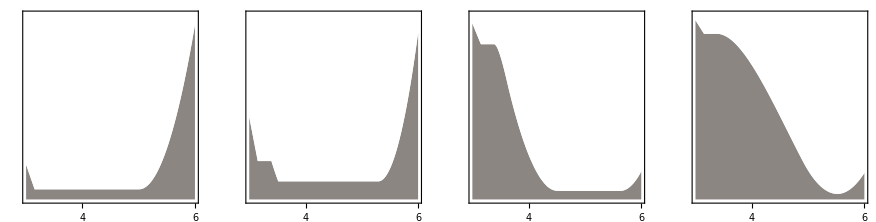

```mathematica
(************** Parameters *******)
c[x_]:=If[x<ThresholdX,cmin,cmax]

cmin=0.05;

ThresholdX=300000;

γ=1;
λf=5;
λs=5;
η=0.1;
P00=0.1;

δ=0.9;

PopSize=1000;
LifeSpan=30;
TimeStep=0.01;

(************** End of Parameters *******)

Tcmax={0.05,0.1,0.5,1};

NbPoints=100;

BackgroundColor=white;
GroundColor=seashell;

seashell="#8B8682";
white="#ffffff";

logzmin=3;
logzmax=6;

MyAspectRatio=1;

For[ii=1,ii≤4,ii++,

cmax=Tcmax[[ii]];
TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];

TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];

TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->6};

Subscript[P, ii]=Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameLabel->{None, None},FrameTicks->{Automatic, None, None, None},LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->200,AspectRatio->MyAspectRatio];];

GraphicsRow[Table[Subscript[P, ii],{ii,1,4}]]
```

Effect of z0 on Lifespan (Figure 5e-h of paper)

## Functions to evaluate before for once (with L that varies with z)

```mathematica
ClearAll["Global`*"]

P[x_,y_,z0_]:=((x^((1-c[x])δ))(y^((c[x])δ)))+P0[z0]

Px[x_,y_]:= -x^(-1+δ-δ c[x]) y^(δ c[x]) δ (-1+c[x]+x (Log[x]-Log[y]) c'[x])
Py[x_,y_]:=x^(δ-δ c[x]) y^(-1+δ c[x]) δ c[x]

xIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[γ thisPx≥λs thisPy,res=γ thisP δt,res=0],
If[γ thisPx≥η thisPy,res=γ thisP δt,res=0]];res];


yIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[λs thisPy > γ thisPx,res=Min[λs thisP δt, z0-y],res=0],
If[η thisPy > γ thisPx,res= (η *λf* thisP * PopSize)/(λf+η(PopSize-1)) δt,res=0]];res];

(*Newz function*)
Newz:=Function[z0,
x=N[10^-10];
y=N[10^-10];
For[t=0,t<LifeSpan[z0],t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]]];
y
];

(*Newz function*)
Adultx:=Function[z0,
x=N[10^-10];
y=N[10^-10];
For[t=0,t<LifeSpan[z0],t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]]];
x
];

Deltaz[z_]:=Newz[z]-z
```

## L increases with z (Figure 5e-h of paper)

#### parameters

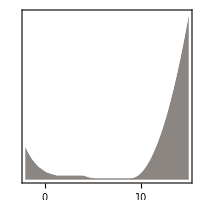

```mathematica
(************** Parameters *******)
P0[z0_]:=P00
c[x_]:=c0
c0=0.5;

γ=1;
λf=5;
λs=5;
η=0.1;
P00=0.1;

δ=0.9;

PopSize=1000;

LifeSpan[z_]:=Lmin+(Lmax-Lmin) z^slope/(ThresholdZ^slope+z^slope) 

Lmin=10;
Lmax=30;
ThresholdZ=10^4;
slope=5;

TimeStep=0.1;


(************** End of Parameters *******)

seashell="#8B8682";
white="#ffffff";

BackgroundColor=white;
GroundColor=seashell;

NbPoints=100;

logzmin=-2;
logzmax=15;


TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];

TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];
TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->10};

Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameLabel->None,LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicks->{Automatic,None,None,None},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->200, AspectRatio->1]
```

#### Variation of Lmax (Figure 5e-h of paper)

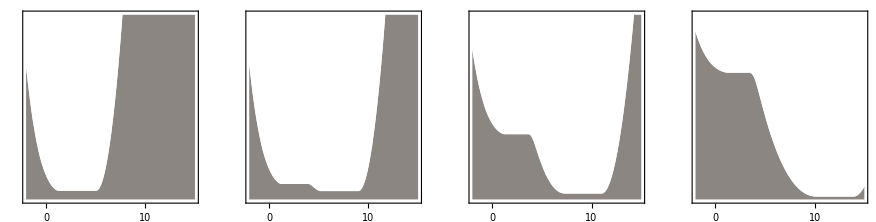

```mathematica
(************** Parameters *******)

P0[z0_]:=P00
c[x_]:=c0
c0=0.5;

γ=1;
λf=5;
λs=5;
η=0.1;
P00=0.1;

δ=0.9;

PopSize=1000;

LifeSpan[z_]:=Lmin+(Lmax-Lmin) z^slope/(ThresholdZ^slope+z^slope) 

Lmin=10;
TLmax={10,30,50,100};
ThresholdZ=10^4;
slope=2;

TimeStep=0.01;

(************** End of Parameters *******)

NbPoints=100;

BackgroundColor=white;
GroundColor=seashell;

seashell="#8B8682";
white="#ffffff";

logzmin=-2;
logzmax=15;

MyAspectRatio=1;

For[ii=1,ii≤4,ii++,

Lmax=TLmax[[ii]];

TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];

TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];
TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
MyRange={{logzmin,logzmax},{Min[TCurve]-1,5}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->6};

Subscript[P, ii]=Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameLabel->{None, None},FrameTicks->{Automatic, None, None, None},LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->200,AspectRatio->MyAspectRatio];];

GraphicsRow[Table[Subscript[P, ii],{ii,1,4}]]
```

λs market effect in z0 (Figure 5i-l of paper)

### Function to evaluate before (with λf != λs)

```mathematica
ClearAll["Global`*"]

P[x_,y_,z0_]:=((x^((1-c[x])δ))(y^((c[x])δ)))+P0[z0]

Px[x_,y_]:= -x^(-1+δ-δ c[x]) y^(δ c[x]) δ (-1+c[x]+x (Log[x]-Log[y]) c'[x])
Py[x_,y_]:=x^(δ-δ c[x]) y^(-1+δ c[x]) δ c[x]


xIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[γ thisPx≥λs[z0] thisPy,res=γ thisP δt,res=0],
If[γ thisPx≥η thisPy,res=γ thisP δt,res=0]];res];


yIncrease:=Function[{x,y,z0, δt},

thisP=P[x,y,z0];
thisPx=Px[x,y];
thisPy=Py[x,y];

If[y<z0,If[λs[z0] thisPy > γ thisPx,res=Min[λs[z0] thisP δt, z0-y],res=0],
If[η thisPy > γ thisPx,res= (η *λf* thisP * PopSize)/(λf+η(PopSize-1)) δt,res=0]];res];

(*Newz function*)
Newz:=Function[z0,
x=N[10^-10];
y=N[10^-10];
For[t=0,t<LifeSpan,t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]]];
y
];

Deltaz[z_]:=Newz[z]-z

ProdFactor[z_]:=max-((max-min)z)/((max-min)/slope+z)
LearnCost[z_]:=z 

ProductionCost[k_,z_]:=UnitaryProdCost  *( k^ProdFactor[z]  )

OptimalDiv[z_]:=(LearnCost[z]/(UnitaryProdCost(ProdFactor[z]-1)))^(1/ProdFactor[z]);(*OptimalDiv represente la division optimale sans contrainte = le nombre de clients optimal par producteur*)

NbProducers[z_]:=If[OptimalDiv[z]<1,PopSize,If[OptimalDiv[z]>PopSize,1,N[PopSize/OptimalDiv[z]]]];(*NbProducers represente le nombre de producteurs necessaires pour fournir tout le monde*)

Price[z_]:=(NbProducers[z] (LearnCost[z]+ProductionCost[ PopSize/NbProducers[z],z]))/PopSize

(*j'ai bien verifié que ça correspond exactemen t au meme p que dans le modele sans contrainte TVTTB*)

λs[z0_]:=Max[λmin,If[z0>0,(λmin z0)/Price[z0],0]]

λf:=λmin
```

### Growth

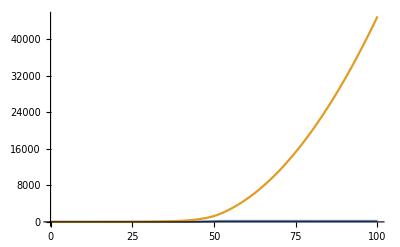

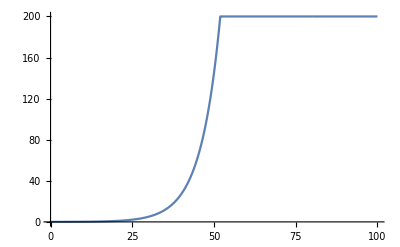

Final x = 45010.7 ; Final y =  200.

```mathematica
(************** Parameters *******)

P0[z_]:=P00
c[x_]:=c0

γ=0.5;
η=10^-3;
P00=0.1;
c0=0.5;

PopSize=1000;
LifeSpan=100;
TimeStep=0.01;
(************** End of Parameters *******)

z0=200;

x=N[10^-10];
y=N[10^-10];
X={{0,x}};
Y={{0,y}};
Ratio={{0,1}};

For[t=0,t<LifeSpan,t+=TimeStep,
x+= N[xIncrease[x,y,z0, TimeStep]];
y+= N[yIncrease[x,y,z0, TimeStep]];
X=Append[X,{t,x}];
Y=Append[Y,{t,y}];
Ratio=Append[Ratio,{t,N[y/x]}]];


ListLinePlot[{Y,X},PlotRange->All]
ListLinePlot[{Y},PlotRange->All]
Print["Final x = ", x, " ; Final y =  ", y];
```

```mathematica
TimeStep=0.1;
Newz[10000]
```

11659.3

### Dynamic landscape (Figure 5i-l of paper)

#### parameters

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

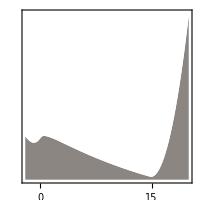

```mathematica
(************** Parameters *******)
slope:=10
max:=2
min:=1

UnitaryProdCost:=1
λmin:=0.01

P0[z_]:=P00
c[x_]:=c0

γ=1;
η=0.1;
P00=0.1;
c0=0.5;

δ=1;

LifeSpan=30;

TimeStep=0.1;

PopSize:=1000;
(************** End of Parameters *******)

seashell="#8B8682";
white="#ffffff";

BackgroundColor=white;
GroundColor=seashell;

NbPoints=100;

logzmin=-2;
logzmax=20;

GroundLevel=2;

TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];
TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
(*MyRange={{logzmin,logzmax},{Min[TCurve]-1,10}};*)

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->10};

Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameTicks->{Automatic,None,None,None},LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->200,AspectRatio->1]
```

#### Variation of PopSize (Figure 5i-l of paper)

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

Less::nord: Invalid comparison with ComplexInfinity attempted.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Less::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

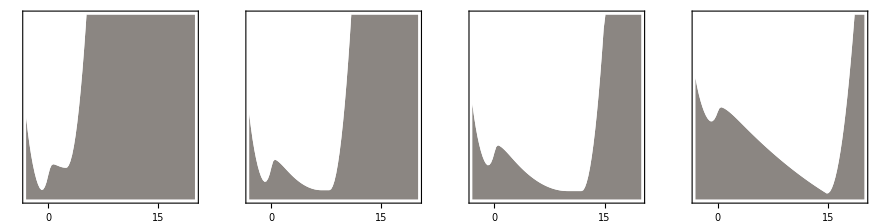

```mathematica
(************** Parameters *******)
slope:=10
max:=2
min:=1

UnitaryProdCost:=1
λmin:=0.01

P0[z_]:=P00
c[x_]:=c0

γ=1;
η=0.1;
P00=0.1;
c0=0.5;

δ=1;

LifeSpan=30;

TimeStep=0.01;

TPopSize={10,50,100,1000};
(************** End of Parameters *******)

seashell="#8B8682";
white="#ffffff";

BackgroundColor=white;
GroundColor=seashell;

NbPoints=100;

logzmin=-3;
logzmax=20;

GroundLevel=1;

For[ii=1,ii≤4,ii++,

PopSize=TPopSize[[ii]];
TLogZ=Table[logz,{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];
TLogNewz=Table[Log[10,Newz[N[10^logz]]],{logz,logzmin,logzmax,(logzmax-logzmin)/(NbPoints-1)}];

TLandscape=Table[{TLogZ[[i]],∑_(k=1)^i (-TLogNewz[[k]]+TLogZ[[k]])+GroundLevel},{i,1,NbPoints}];

TCurve=Table[TLandscape[[i,2]],{i,1,NbPoints}];
MyRange={{logzmin,logzmax},{Min[TCurve]-1,Max[TCurve]+1}};
MyRange={{logzmin,logzmax},{Min[TCurve]-1,10}};
GroundLevel=1;

PInverseLandscape1=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Bottom,FillingStyle->RGBColor[GroundColor]];

PInverseLandscape2=ListLinePlot[TLandscape,PlotRange->MyRange,PlotStyle->{Opacity[0],RGBColor[GroundColor]}, Filling->Top,FillingStyle->RGBColor[BackgroundColor]];

MyTicks={FontFamily->"Avenir",FontSize->6};

Subscript[P, ii]=Show[PInverseLandscape1,PInverseLandscape2,Axes->False,Frame->True,PlotRange->MyRange,FrameTicks->{Automatic, None, None, None},LabelStyle->{FontFamily->"Avenir",FontSize->12},FrameTicksStyle->{MyTicks,MyTicks,MyTicks,MyTicks},ImageSize->200,AspectRatio->1];];

GraphicsRow[Table[Subscript[P, ii],{ii,1,4}]]
```

## Division of labour / Market

People make an optimal social contract = 

they divide the work cooperatively =

1) they define a selling price so that everyone can understand it (no one regrets not having become a producer or vice versa)

2) they choose the number of producers such that the selling price is minimal (the cost of the good for each one is minimized)

If we have n producers and a selling price p, each producer produces and sells N/n goods; including to himself with a profit b

The gain for producers is therefore

```mathematica
G=N/n p - l-c(N/n)^a + b-p
```

while the gain for pure consumers is

```mathematica
C=b-p
```

So equilibrium implies that everyone earns the same so that the cost of production is totally compensated by the profits from the sale ==> implies that the price is such that

```mathematica
Solve[N/n p - l-c(N/n)^a==0,p]
```

{{p→(n (l+c (N/n)^a))/N}}

so that gives us a price if we have no producers.

in this case the net gain of each individual will be exactly

```mathematica
b-p
```

In other words, p corresponds to the cost of production equally shared by everyone in the population, so the most advantageous arrangement is the one that minimizes the price p!

So we are looking for the number of producers n such that p[n] is minimized; so this gives us ==>

```mathematica
p[n_]:=(n (l+c (N/n)^a))/N
```

```mathematica
D[p[n],n]//FullSimplify
```

(l-(-1+a) c (N/n)^a)/N

```mathematica
Solve[l-(-1+a) c (N/n)^a==0,n]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→(l/((-1+a) c))^(-1/a) N}}

So we get the optimal division of labor

```mathematica
s:=(l/(c(a-1)))^(1/a)
```

and the actual division of labour is given by

n=N/s  if s \in [1, N]
n=N if s<1
n=1 if s>N

In the case where the number of producers is large, this approach gives the same result than in a perfect competitive market.

But our approach allows us to be more general and take into accounts constraints on the division of labor that stem from the discete nature of individuals (the minimum number of producers is 1 which puts an upper limit on the division of labor).
The cost of a cultural item is given by p with

```mathematica
ClearAll["Global`*"]
s:=(l/(c(a-1)))^(1/a)
n[s_]:=If[s<1,PopSize,If[s>PopSize,1,PopSize/s]]
p[n_]:=(n (l+c (PopSize/n)^a))/PopSize
```